```mathematica
x={
-5.22,-9.28,-2.54,-4.76,-1.18,-2.78,-5.89,-6.87,-3.01,1.70,
-4.59,-1.59,-6.16,2.83,-3.59,2.29,-2.20,-0.37,-5.14,-0.72,
-2.22,-1.97,1.00,1.67,-1.79,-2.74,-4.49,-0.67,4.68,-5.87,
-1.38,-5.34,-4.17,-4.14,-2.58,-0.35,-2.24,1.57,1.37,-2.05,
0.88,-2.16,-11.60,-5.74,-4.86,-2.23,-4.14,-0.79,-2.54,-4.65
}
```

{-5.22,-9.28,-2.54,-4.76,-1.18,-2.78,-5.89,-6.87,-3.01,1.7,-4.59,-1.59,-6.16,2.83,-3.59,2.29,-2.2,-0.37,-5.14,-0.72,-2.22,-1.97,1.,1.67,-1.79,-2.74,-4.49,-0.67,4.68,-5.87,-1.38,-5.34,-4.17,-4.14,-2.58,-0.35,-2.24,1.57,1.37,-2.05,0.88,-2.16,-11.6,-5.74,-4.86,-2.23,-4.14,-0.79,-2.54,-4.65}

```mathematica
(*Строим вариационный ряд реализации*)
```

```mathematica
x=Sort[x]
```

{-11.6,-9.28,-6.87,-6.16,-5.89,-5.87,-5.74,-5.34,-5.22,-5.14,-4.86,-4.76,-4.65,-4.59,-4.49,-4.17,-4.14,-4.14,-3.59,-3.01,-2.78,-2.74,-2.58,-2.54,-2.54,-2.24,-2.23,-2.22,-2.2,-2.16,-2.05,-1.97,-1.79,-1.59,-1.38,-1.18,-0.79,-0.72,-0.67,-0.37,-0.35,0.88,1.,1.37,1.57,1.67,1.7,2.29,2.83,4.68}

```mathematica
(*Находим оптимальную величину интервала по правилу Старджеса*)
```

```mathematica
Δt=(x[[Length[x]]]-x[[1]])/(1+Log2[Length[x]])
```

2.45038

```mathematica
Clear[k];
```

```mathematica
(*Номер относительно нуля крайнего слева интервала*)
```

```mathematica
kStart=k/.(Maximize[k,Reduce[Δt k<x[[1]],k,Integers],k][[2]])
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-5

```mathematica
(*Номер относительно нуля крайнего справа интервала*)
```

```mathematica
kEnd=(k/.(Minimize[k,Reduce[Δt k>x[[Length[x]]],k,Integers],k][[2]]))-1
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1

```mathematica
(*Частота*)
```

```mathematica
Rate[data_,start_,end_]:=(
count=0;
For[ii=1,ii≤Length[data],ii++,
If[IntervalMemberQ[Interval[{start,end}],data[[ii]]],count++;];
];
Return[count];
);
```

```mathematica
(*Составляем первую таблицу*)
```

```mathematica
table={};
For[i=kStart,i≤kEnd,i++,
AppendTo[table,{(i+1)-kStart,i Δt,(i+1) Δt,(i Δt + (i+1) Δt)/2,Rate[x,i Δt,(i+1) Δt],Rate[x,i Δt,(i+1) Δt]/Length[x]}];
];
TableForm[table,
TableHeadings->{None,{"№","Начало","Конец","Середина","Частота","Частость"}}]
```

№ | Начало | Конец | Середина | Частота | Частость
1 | -12.2519 | -9.80154 | -11.0267 | 1 | 1/50
2 | -9.80154 | -7.35115 | -8.57634 | 1 | 1/50
3 | -7.35115 | -4.90077 | -6.12596 | 8 | 4/25
4 | -4.90077 | -2.45038 | -3.67558 | 15 | 3/10
5 | -2.45038 | 0. | -1.22519 | 16 | 8/25
6 | 0. | 2.45038 | 1.22519 | 7 | 7/50
7 | 2.45038 | 4.90077 | 3.67558 | 2 | 1/25

```mathematica
(*Составляем вторую таблицу*)
```

```mathematica
For[iii=1,iii≤Length[table]-1,iii++,
If[table[[iii]][[5]]<5,
tmptable=Join[
If[iii>1,Part[table,1;;(iii-1)],{}],
{{0,table[[iii]][[2]],table[[iii+1]][[3]],(table[[iii]][[2]]+table[[iii+1]][[3]])/2,table[[iii]][[5]]+table[[iii+1]][[5]],table[[iii]][[6]]+table[[iii+1]][[6]]}},
If[iii<Length[table]-1,Part[table,(iii+2);;Length[table]],{}]
];
table=tmptable;
iii=0;
];
];
(*Отдельно проверка для последней строки и, если требуется, объединение ее с предпоследней*)
If[table[[Length[table]]][[5]]<5,
tmptable=Join[
Part[table,1;;(Length[table]-2)],
{{0,table[[Length[table]-1]][[2]],table[[Length[table]]][[3]],(table[[Length[table]-1]][[2]]+table[[Length[table]]][[3]])/2,table[[Length[table]-1]][[5]]+table[[Length[table]]][[5]],table[[Length[table]-1]][[6]]+table[[Length[table]]][[6]]}}
];
table=tmptable;
];
For[j=1,j≤Length[table],j++,
table[[j]][[1]]=j;
];
```

```mathematica
TableForm[table,
TableHeadings->{None,{"№","Начало","Конец","Середина","Частота","Частость"}}]
```

№ | Начало | Конец | Середина | Частота | Частость
1 | -12.2519 | -4.90077 | -8.57634 | 10 | 1/5
2 | -4.90077 | -2.45038 | -3.67558 | 15 | 3/10
3 | -2.45038 | 0. | -1.22519 | 16 | 8/25
4 | 0. | 4.90077 | 2.45038 | 9 | 9/50

```mathematica
(*Находим a и σ^2 по формулам*)
```

```mathematica
a=1/Length[x]∑_(i=1)^Length[table] table[[i]][[4]] table[[i]][[5]]
```

-2.76893

```mathematica
σ=√(1/Length[x]∑_(i=1)^Length[table] (table[[i]][[4]]-a)^2 table[[i]][[5]])
```

3.55779

```mathematica
σ^2
```

12.6578

```mathematica
(*Выборочное среднее*)
```

```mathematica
X̄=Total[x]/Length[x]
```

-2.5722

```mathematica
(*Выборочная дисперсия*)
```

```mathematica
S=√(1/Length[x]∑_(i=1)^Length[x] (x[[i]]-X̄)^2)
```

3.05669

```mathematica
(*Чертеж гистограммы, полигона частот и плотности*)
```

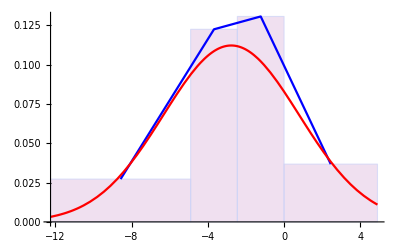

```mathematica
Show[
Histogram[x,{Join[Table[table[[i]][[2]],{i,1,Length[table]}],{table[[Length[table]]][[3]]}]},"PDF",PlotRange->All,ChartStyle->LightPurple],
ListLinePlot[{Table[{table[[i]][[4]],(table[[i]][[6]])/(table[[i]][[3]]-table[[i]][[2]])},{i,1,Length[table]}]},PlotStyle->Directive[Blue,Thickness[0.004]],PlotRange->All],
Plot[PDF[NormalDistribution[a,σ],x],{x,kStart Δt,(kEnd+1) Δt},PlotStyle->{Red,Thickness[0.004]},PlotRange->All]
]
```

```mathematica
(*Доверительный интервал для среднего*)
```

```mathematica
aCI=Interval[{X̄-Quantile[StudentTDistribution[Length[x]-1],(1+0.95)/2] S/(√(Length[x]-1)),X̄+Quantile[StudentTDistribution[Length[x]-1],(1+0.95)/2] S/(√(Length[x]-1))}]
```

Interval[{-3.44972,-1.69468}]

```mathematica
(*Доверительный интервал для дисперсии*)
```

```mathematica
σCI=Interval[{(Length[x] S^2)/Quantile[ChiSquareDistribution[Length[x]-1],(1+0.95)/2],(Length[x] S^2)/Quantile[ChiSquareDistribution[Length[x]-1],(1-0.95)/2]}]
```

Interval[{6.6527,14.8049}]

```mathematica
(*Проверка гипотезы о нормальном распределении выборки с помощью критериев согласия Колмогорова и χ^2 Пирсона*)
```

```mathematica
ℋ=DistributionFitTest[x,NormalDistribution[X̄,S],"HypothesisTestData"];
```

```mathematica
TableForm[{{"Колмогоров",ℋ["TestStatistic","KolmogorovSmirnov"],"t√n",ℋ["TestStatistic","KolmogorovSmirnov"] √Length[x],"","λ_0.05",1.6449},
{"Пирсон", ℋ["TestStatistic","PearsonChiSquare"],"t",ℋ["TestStatistic","PearsonChiSquare"],"","χ_(0.95, N - 1)^2",Quantile[ChiSquareDistribution[Length[table]-1],0.95]}},
TableHeadings->{None,{"","Статистика","Левая часть неравенства",SpanFromLeft,"< ⇒ OK","Правая часть неравенства",SpanFromLeft}}]
```

DistributionFitTest::ties: Ties exist in the data and will be ignored for the {"KolmogorovSmirnov"} test, which assumes unique values.

| Статистика | Левая часть неравенства |  | < ⇒ OK | Правая часть неравенства | 
Колмогоров | 0.0729 | t√n | 0.515481 |  | λ_0.05 | 1.6449
Пирсон | 7.6 | t | 7.6 |  | χ_(0.95, N - 1)^2 | 7.81473

```mathematica
ℋ["TestConclusion","KolmogorovSmirnov"]
```

DistributionFitTest::ties: Ties exist in the data and will be ignored for the {"KolmogorovSmirnov"} test, which assumes unique values.

The null hypothesis that the data is distributed according to the NormalDistribution[-2.5722,3.05669] is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

```mathematica
ℋ["TestConclusion","PearsonChiSquare"]
```

The null hypothesis that the data is distributed according to the NormalDistribution[-2.5722,3.05669] is not rejected at the 5 percent level based on the Pearson χ^2 test.

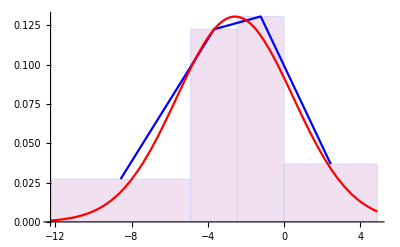

```mathematica
Show[Histogram[x,{Join[Table[table[[i]][[2]],{i,1,Length[table]}],{table[[Length[table]]][[3]]}]},"ProbabilityDensity",ChartStyle->LightPurple],
ListLinePlot[{Table[{table[[i]][[4]],(table[[i]][[6]])/(table[[i]][[3]]-table[[i]][[2]])},{i,1,Length[table]}]},PlotStyle->Directive[Blue,Thickness[0.004]],PlotRange->All],
Plot[PDF[ℋ["FittedDistribution"],x],{x,kStart Δt,(kEnd+1) Δt},PlotStyle->{Red,Thickness[0.004]}]]
```